```mathematica
(*Code created by Loïc Marrec*)
```

```mathematica
(*Description:Fixation time in the stepping stone model*)
```

```mathematica
(*PARAMETERS*)
```

```mathematica
bW=1;(*Wild-type birth rate*)
```

```mathematica
dW=0.1;(*Wild-type death rate*)
```

```mathematica
bM=Table[i,{i,0.95,1.1,0.001}];(*Mutant birth rates*)
```

```mathematica
dM=0.1;(*Mutant death rate*)
```

```mathematica
Δ=5;(*Number of demes*)
```

```mathematica
κ=100;(*Carrying capacity*)
```

```mathematica
(*EQUILIBRIUM DEME SIZES*)
```

```mathematica
NW=κ*(1-dW/bW);(*Wild-type deme equilibrium size*)
```

```mathematica
NM=Table[κ*(1-dM/bM[[i]]),{i,Length[bM]}];(*Mutant deme equilibrium sizes*)
```

```mathematica
(*FIXATION PROBABILITIES WITHIN DEMES*)
```

```mathematica
uW=Table[If[bM[[i]]==bW*dM/dW,1/NM[[i]],(1-(bM[[i]]*dW)/(bW*dM))/(1-((bM[[i]]*dW)/(bW*dM))^NM[[i]])],{i,Length[bM]}];(*Fixation probability of a wild type in a mutant deme*)
```

```mathematica
uM=Table[If[bM[[i]]==bW*dM/dW,1/NW,(1-(bW*dM)/(bM[[i]]*dW))/(1-((bW*dM)/(bM[[i]]*dW))^NW)],{i,Length[bM]}];(*Fixation probability of a mutant in a wild-type deme*)
```

```mathematica
(*DISPERSAL PARAMETERS*)
```

```mathematica
mW={0.000005,0.000002,0.000001,0.000001,0.000001};(*Wild-type dispersal rates*)
```

```mathematica
mM={0.000001,0.000001,0.000001,0.000002,0.000005};(*Mutant dispersal rates*)
```

```mathematica
α=mM/mW;(*Ratio of dispersal rates*)
```

```mathematica
(*RELATIVE FITNESS OF MUTANT DEMES*)
```

```mathematica
r=Table[α[[j]]*(NM[[i]]*uM[[i]])/(NW*uW[[i]]),{i,Length[bM]},{j,Length[α]}];
```

```mathematica
(*GLOBAL FIXATION TIMES*)
```

```mathematica
tfix=Table[If[r[[i,j]]==1,(Δ^2-1)/(6*mM[[j]]*uM[[i]]*NM[[i]]),(r[[i,j]]*(1+r[[i,j]]+r[[i,j]]^Δ*(-1+r[[i,j]]*(-1+Δ)-Δ)-Δ+r[[i,j]]*Δ))/(mM[[j]]*(r[[i,j]]-1)^2*(r[[i,j]]^Δ-1)*uM[[i]]*NM[[i]])],{i,Length[bM]},{j,Length[α]}];
```

```mathematica
(*DATA PREPARATION AND VISUALIZATION*)
```

```mathematica
tfixtable=Table[{bM[[j]]/bW-1,tfix[[j,i]]},{i,1,Length[α]},{j,1,Length[bM]}];(*Selection coefficient vs.fixation time*)
```

```mathematica
colorRain=Table[ColorData["Rainbow"][k],{k,0,1,1/(Length[α]-1)}];(*Color gradient for plots*)
```

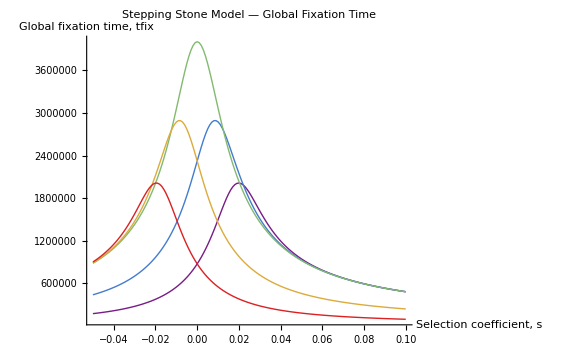

```mathematica
Show[Table[ListPlot[tfixtable[[f]],PlotStyle->{colorRain[[f]],Thick},Joined->True],{f,1,Length[α]}],PlotLabel->"Stepping Stone Model — Global Fixation Time",PlotRange->All,AxesLabel->{"Selection coefficient, s","Global fixation time, tfix"},ImageSize->Large]
```